# Mathematica Plotting and Manipulate

## Plotting Functions

Mathematica contains a plethora of graphing functions: 
Plot
 PolarPlot
 ListPlot
 Plot3D
 ParametricPlot
  LogPlot 
  ListLinePlot
  LogLogPlot
  ContourPlot
  The list goes on and on....
  
  One great and quite way to visualize physical problems is to use one of the plotting tools with Mathematica’s Manipulate Function.

### Plot

Plot is the basic graphing function in Mathematica

```mathematica
Plot[Sin[x],{x,0,4π}]
```

```mathematica
Plot[Sin[x],{x,0,4π},AxesLabel->{x,Sin[x]},LabelStyle->Directive[Bold,Large]]
Plot[Sin[x],{x,0,4π},AxesLabel->{"x","Sin[x]"},LabelStyle->Red]
Plot[Sin[x],{x,0,4π},AxesLabel->{Rotate["x-axis",90 Degree],"Sin[x]"}]
Plot[Sin[x]^2,{x,0,4π},AxesLabel->{Subscript["x",0],Superscript["Sin",2]["x"]}]
```

### PolarPlot

PolarPlot allows you to plot in a 2D polar plotting space. PolarPlot uses basic commands similar to Plot.

```mathematica
PolarPlot[5,{x,0,6π},AxesLabel->{"x","y"}]
```

```mathematica
PolarPlot[θ,{θ,0,6 Pi},PlotStyle->Thick,ColorFunction->Function[{θ,r},Hue[θ/(2 Pi)]],ColorFunctionScaling->False]
```

### ParametricPlot

ParametricPlot allows you to plot parametric functions in the xy plane using a third parameter.

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->Thick,AxesLabel->{"x","y"}]
```

```mathematica
ParametricPlot[{Sin[t]+t Cos[t],Cos[t]-t Sin[t]},{t,0,6 Pi},PlotStyle->Thick,AxesLabel->{"x","y"},PlotRange->All,ColorFunction->"Rainbow"]
```

### Listplots

Mathematica allows you to plot analytical functions and lists of numbers

```mathematica
y = Range[25];
y2={3,2,5,8,0,1,10,34,67,89,4};
ListPlot[y]
ListPlot[y2]
ListPlot[Table[Style[{Cos[t],Sin[2 t]}],{t,0,2 Pi,Pi/20}],PlotStyle->PointSize[Medium]]
```

```mathematica
ListPlot[{Labeled[Sqrt[y],"sqrt"],Labeled[Log[y],"log"]}]
```

```mathematica
ListPlot[{Labeled[Sqrt[y2],"sqrt"],Labeled[Log[y2],"log"]}]
```

```mathematica
ListLinePlot[y2]
```

### Plot3D

Mathematica can produce 3D graphics.

```mathematica
Plot3D[Sin[x] Cos[y],{x,-Pi,Pi},{y,-Pi,Pi}]
Plot3D[Sin[x] Cos[y],{x,-Pi,Pi},{y,-Pi,Pi},ColorFunction->Function[{x,y,z},ColorData["SunsetColors"][z]],Mesh->None,Boxed->False,AxesLabel->{"x","y","z"}]
Plot3D[Sin[x] Cos[y],{x,-Pi,Pi},{y,-Pi,Pi},ColorFunction->Function[{x,y,z},ColorData["SunsetColors"][z]],Mesh->None,Boxed->False,AxesLabel->{"x","y","z"},Axes->False]
```

### Contour Plot

Contour plots allow you to represent three dimensional data in two dimensional surfaces using contour lines, which connect points of equal value. Examples include topographical maps and electric potential graphs.

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5}]
```

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5},ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic]]
```

```mathematica
ContourPlot[Sin[x] Cos[y],{x,-Pi,Pi},{y,-Pi,Pi},Contours->16 ]
```

```mathematica
ContourPlot[Sin[x] Cos[y],{x,-Pi,Pi},{y,-Pi,Pi},Contours->10,ContourShading->None,FrameLabel->{"x","y"}]
```

```mathematica
ContourPlot[Sin[x] Cos[y],{x,-Pi,Pi},{y,-Pi,Pi},Contours->10,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{ColorData["TemperatureMap"],{-1,1}},LabelStyle->{Bold,14},LegendLabel->"Magnitude"]]
```

### Region Plots

RegionPlot is a function allowing you to visualize regions that satisfy inequalities or conditions in two variables. This could be useful in displaying solution sets, feasible regions or any example needing a clear picture where conditions hold true in a coordinate plane.

```mathematica
RegionPlot[x^2+y^2<1,{x,-1.5,1.5},{y,-1.5,1.5}]
```

```mathematica
RegionPlot[x^2+y^2<1&&x+y>0,{x,-1.5,1.5},{y,-1.5,1.5},PlotStyle->LightBlue,AxesLabel->{"x","y"}]
```

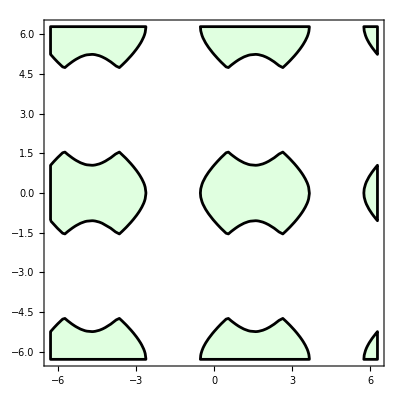

```mathematica
RegionPlot[Sin[x]+Cos[y]>0.5&&Sin[x]-Cos[y]<0.5,{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},PlotStyle->LightGreen,BoundaryStyle->Black]
```

### Manipulate

Manipulate is a fast versatile way of creating dynamic expressions, graphs, and other visuals . You can use Manipulate with any function (s) to vary parameters and produce the modified results.

```mathematica
Manipulate[Plot[A Sin[x],{x,0,2 Pi},PlotRange->{-2,2}],{A,-2,2}]
```

```mathematica
Manipulate[Plot[A Sin[B x+C],{x,0,2 Pi},PlotRange->{-2,2},PlotLabel->Row[{"A Sin[B x + C]"}]],{A,0.5,2},{B,1,5},{C,0,2 Pi}]
```

## Examples used to Illustrate Physical Phenomena

### Elliptical Orbits

Most bodies in our solar system follow an elliptical orbit. We can get an idea about how the eccentricity warps the orbit from a purely circular one by graphing the orbital equations in polar coordinates

```mathematica
Manipulate[PolarPlot[{1/(1+ϵ Cos[ϕ]),R},{ϕ,0,2π}],{ϵ,0,1.5},{R,1,10}]
```

### Precession of the Perihelion

The perihelion of many bodies precesses about the elliptical orbit’s focus (a famous example being the precession of Mercury’s perihelion). We can use PolarPlot with Manipulate to visualize this precession.

```mathematica
Manipulate[PolarPlot[{1/(1+ϵ Cos[ϕ+a])},{ϕ,0,2π}, PlotRange->{{-8,8},{-8,8}}],{ϵ,0,1},{a,0,4*π}]
```

### Charged Particles in Electric and Magnetic Fields

Charged particles in a magnetic field undergo circular motion and those in an electric field are acceleration along the field lines. The combined motion can be described as undergoing helical motion. What does that look like?

```mathematica
qm=10;
time[Bx_,By_,Bz_] := (20 π)/(qm*√(Bx^2+By^2+Bz^2));
motion[Ex_,Ey_,Ez_,Bx_,By_,Bz_,vx0_,vy0_,vz0_]:=NDSolve[{vx'[t]==qm*Ex - qm(vy[t]Bz - vz[t]By),vy'[t]==qm*Ey - qm(vz[t]Bx - vx[t]Bz),vz'[t]==qm*Ez - qm(vx[t]By - vy[t]Bx),vx[0]==vx0,vy[0]==vy0,vz[0]==vz0},{vx[t],vy[t],vz[t]},{t,0,time[Bx,By,Bz]}]
```

```mathematica
vel = motion[10,20,64,0.5,0.21,0.23,2,2,2]
```

```mathematica
vel[[1,1]]
```

```mathematica
ParametricPlot3D[{{vx[t]/.vel[[1,1]],vy[t]/.vel[[1,2]],vz[t]/.vel[[1,3]]},{t,0,0}},{t,0,time[0.5,0,0]}]
```

### Fluid Dynamics

A classic problem in fluid dynamics involves a water tank with diameter d_t and height H and pressurized to a gauge pressure of P. You cut a small hole of diameter d_bin the bottom of the tank.  Using Bernoulli’s principle and the continuity equation, you can express the time it takes to empty such a tank to empty. It should be obvious (if you review the relevant topics) that a tank does not empty as a constant rate, it necessitates calculus. The expression for the rate at which the surface of the water in the tank falls is given by

dh/dt = (√(2 P/ρ+2gh))/((d_t/d_b)^2+1)

To solve such an equation, we need to separate the differentials and integrate

```mathematica
Clear[g]
T[P_,ρ_,dt_,db_,h_]=Integrate[(dt^2/db^2+1)/(√(2*P/ρ+2*g*h)),h]
```

We can graph the function T and without filling in the parameters inside Manipulate to see how different parameters affect the time to empty

```mathematica
g=9.81;
Manipulate[Plot[T[P,ρ,dt,db,h],{h,0,1.5},AxesLabel->{"Height (m)","Time to empty (s)"}],{P,0,10000},{ρ,500,1500},{db,1,10},{dt,200,500}]
```

We can even use Manipulate with regular evaluations

```mathematica
Manipulate[(T[P,ρ,dt,db,h]-T[P,ρ,dt,db,0])/60,{P,5000,10000},{ρ,500,1500},{dt,1,50},{db,0.01,0.5},{h,0.1,3.0}]
```

```mathematica
T[5000,1000,1.7,0.014,0.9]/60
```

### Random Examples

```mathematica
VectorPlot3D[{x, y, z}, {x, -3, 3}, {y, -3, 3}, {z, -3, 3}, 
 VectorColorFunction -> “DeepSeaColors”]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t], Sin[t], t/10}, {t, 0, 20 Pi}, 
 PlotStyle -> Thick, ColorFunction -> Function[{x, y, z, t}, Hue[t/(20 Pi)]], 
 ColorFunctionScaling -> False, 
 Boxed -> False, Axes -> False]
```

-Graphics3D-

```mathematica
Manipulate[
 VectorPlot3D[{a y, -a x, b z}, {x, -2, 2}, {y, -2, 2}, {z, -2, 2}, 
  VectorStyle -> "Arrow3D", VectorScale -> {Small, 0.5, None},Boxed -> False, Axes -> True, 
  PlotRange -> {{-2, 2}, {-2, 2}, {-2, 2}}],
 {a, 0, 2, 0.1, Appearance -> "Labeled"},
 {b, -1, 1, 0.1, Appearance -> "Labeled"}
]
```